```mathematica
D[ρ[r]*u[r],r] + ρ[r]*u[r]/r
D[ρ[r]*u[r]^2 + p[r],r] + ρ[r]*u[r]^2/r 
D[ρ[r]*u[r]^3 /2+ γ*u[r]*p[r]/(γ-1),r] + ρ[r]*u[r]^3/(2*r) +γ*u[r] p[r]/(γ-1)/r
```

(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]

(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]

(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]

```mathematica
Решаем
```

```mathematica
γ=2.0;
r1=0.13;
F=8;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[0.1]==1,ρ[0.1]==1,p[0.1]==0.05},{ρ,u,p},{r,0.1,r1}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
""
```

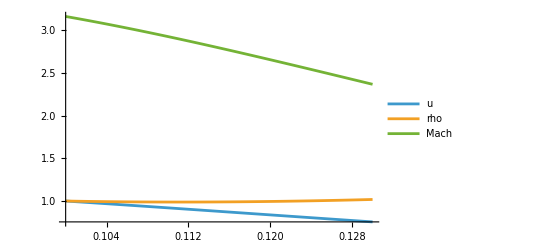

```mathematica
Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","Mach"}]
```

```mathematica
DD = 0;
ro1 =ρ[r1]/. s
p1 = p[r1]/. s
u1 = u[r1]/. s
g = 2.0;
ss = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 == ro*u*(u - DD)+ p&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals]
```

{1.01822}

{0.0518386}

{0.755467}

{{p→0.370139,ro→2.25135,u→0.341676},{p→0.0518386,ro→1.01822,u→0.755467}}

```mathematica
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
r2=0.8;
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]u[r]/ρ[r],u[r1]==g1,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

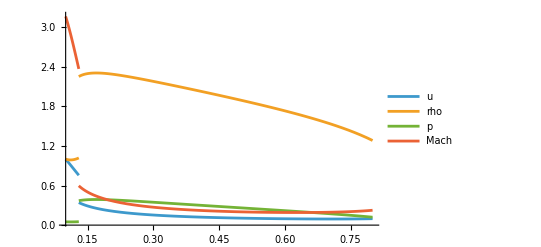

```mathematica
Show[Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[p[r]/. s],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","p","Mach"}],Plot[{Evaluate[u[r]/. sss],Evaluate[ρ[r]/. sss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. sss]},{r,r1,r2},PlotRange->All]]
```

```mathematica
g1=u[r2]/. sss;
g2=ρ[r2]/. sss;
g3=p[r2]/. sss;
r3=0.583;
ssss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F/u[r]*ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]/u[r]*ρ[r],u[r2]==g1,ρ[r2]==g2,p[r2]==g3},{ρ,u,p},{r,r2,r3}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.300006} lies outside the range of data in the interpolating function. Extrapolation will be used.

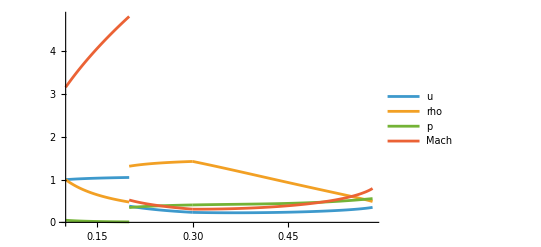

```mathematica
Show[Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[p[r]/. s],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","p","Mach"}],Plot[{Evaluate[u[r]/. sss],Evaluate[ρ[r]/. sss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. sss]},{r,r1,r2},PlotRange->All],Plot[{Evaluate[u[r]/. ssss],Evaluate[ρ[r]/. ssss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. ssss]},{r,r2,r3},PlotRange->All]]
```

```mathematica
xValues=Range[0.17,0.8,0.15]; (*шаг 0.1*)
pValues=u[xValues]/. sss;
Export["D:sss.csv",pValues,"CSV"];
xValues
pValues
```

{0.17,0.32,0.47,0.62,0.77}

{{0.310108,0.16538,0.121538,0.101124,0.0916454}}

```mathematica
T = {{0.17,0.31010790623201573},{0.32,0.16537987485834005},{0.47,0.12153843156423706},{0.7700000000000001,0.09164542330087837}};
poly=InterpolatingPolynomial[T,r]
```

0.0916454+(-0.364104+(0.881536-3.02309 (-0.47+r)) (-0.17+r)) (-0.77+r)

```mathematica
0.1373819908048013+(-0.1812890357271155+(-0.5476813166387459+1.3895503902487591 (-0.37+r)) (-0.17+r)) (-0.7700000000000001+r)
```